# Fitting by multiple NMR

{0.664617,0.571336,0.567985,0.532493,0.559153}

0.579117

FittedModel[7.20252-0.558858 x]

0.571862

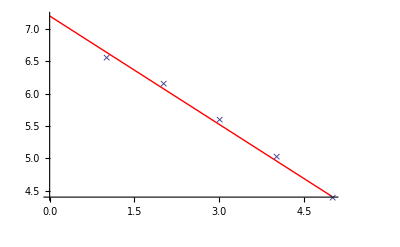

```mathematica
L={699.2,
464.7,
265.5,
150.8,
80.3,
44.9};
LR=Table[N[L[[n+1]]/L[[n]],10],{n,1,Length[L]-1}]
m=Mean[LR]
J=LinearModelFit[Log[L],x,x]
Exp[J[1]-J[0]]
Show[Plot[Normal[J],{x,0,5},PlotStyle->Red],ListLogPlot[L,PlotMarkers-> {"×",Large}]]
```

```mathematica
K={0.394, 0.278,0.124, 36.2/632.2, 91/626.2, 147.8/610.3}
```

{0.394,0.278,0.124,0.0572604,0.145321,0.242176}

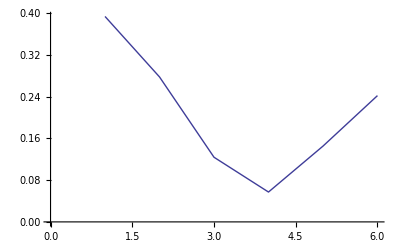

```mathematica
ListLinePlot[K]
```